## Q1: Zeros of the Bessel Function

We find the first three zeros of the Bessel function :

```mathematica
Solve[BesselJ[1, x] == 0, Assumptions -> x >= 0];
x /. %[[1]]
N[x/.%%[[2]]/.{C[1]->1}]
N[x/.%%%[[2]]/.{C[1]->2}]
```

0

3.83171

7.01559

## Q2: Integrals and derivatives

We want to integrate and then take the derivative of the expression :

```mathematica
f[x_]:= ⅇ^x Sin[x];
F[x_]:=Integrate[f[x], x]
F[x]
D[F[x], x]//Simplify
```

1/2 ⅇ^x (-Cos[x]+Sin[x])

ⅇ^x Sin[x]

## Q3: Solution of transcendental equation

We solve, both symbolically and numerically, the equation . First we make a plot:

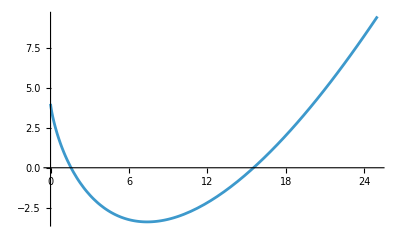

```mathematica
Plot[x Log[x]-3 x +4, {x, 0, 25}]
```

Now we search for the analytic solutions:

```mathematica
Solve[x Log[x]-3 x +10 == 6]//N
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→15.5229},{x→1.56883}}

And the numeric solutions:

```mathematica
NSolve[x Log[x]-3 x +10 == 6]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1.56883},{x→15.5229}}

which coincide!

## Q4: Solution to differential equations

We search for the solution, analytically and numerically, of the following Cauchy problem:

```mathematica
DSolve[{y''[x]-x y[x] == 0, y[0]==0, y'[0]== -3^(1/3)Gamma[2/3]/Gamma[1/3]}, y[x], {x, 0, 5}];
sol[x_]= y[x]/.%[[1]]
```

1/2 3^(1/6) (√3 AiryAi[x]-AiryBi[x]) Gamma[2/3]

```mathematica
NDSolve[{y''[x]-x y[x] == 0, y[0]==0, y'[0]== -3^(1/3)Gamma[2/3]/Gamma[1/3]}, y[x], {x, 0, 5}];
solnum[x_]=y[x]/.%[[1]]
```

InterpolatingFunction[…][x]

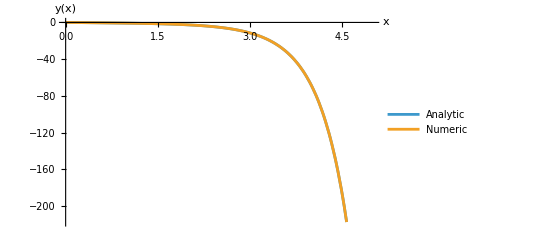

```mathematica
Plot[{sol[x], solnum[x]}, {x, 0, 5}, PlotLegends->{"Analytic", "Numeric"}, AxesLabel->{"x", "y(x)"}]
```

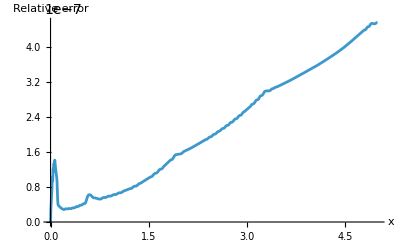

```mathematica
Plot[Abs[(sol[x]-solnum[x])/sol[x]], {x, 0, 5}, AxesLabel->{"x", "Relative error"}]
```